## Backgrounds for my Web Page

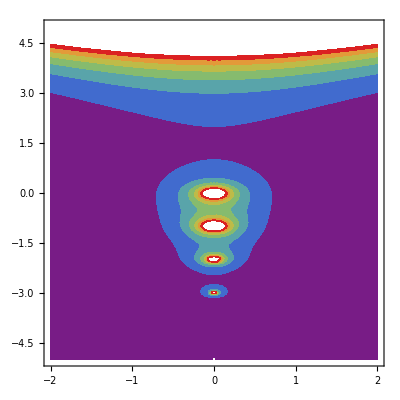

```mathematica
ContourPlot[Abs[Gamma[y+ⅈ x]],{x,-2,2},{y,-5,5},ContourStyle->None,ColorFunction->"Rainbow",ImageSize->Full]
```

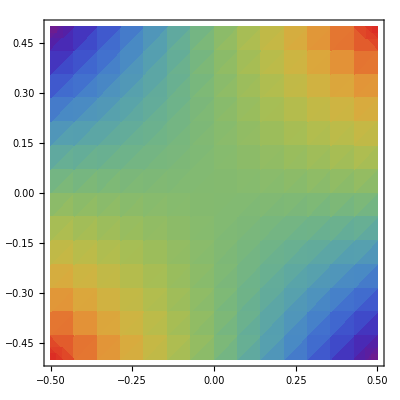

```mathematica
DensityPlot[Sin[x y],{x,-.5,.5},{y,-.5,.5},ColorFunction->"Rainbow",ImageSize->Full]
```

## Interpret a single move command and update the current location and direction. Lpos = global position Ltheta = global direction

```mathematica
Lmove[ z_String, Ldelta_ ] :=
    Switch[ z,
        "+", Ltheta += Ldelta;,
        "-", Ltheta -= Ldelta;,
        "F", Lpos += {Cos[Ltheta], Sin[Ltheta]},
        "B", Lpos -= {Cos[Ltheta], Sin[Ltheta]},
         _ ,   Lpos += 0. ]
```

## Create the string S starting with the string axiom, expanding according to production rules n times.

```mathematica
LSystem::usage =
    "LSystem[axiom, {rules}, n, Ldelta:90 Degree]
    creates the L-string for the nth iteration of
    the list 'rules', starting with the string 'axiom'.";
```

```mathematica
LSystem[ axiom_, 
            rules_List,
                   n_Integer, 
            Ldelta_:N[90 Degree]
          ] :=    
    Nest[ StringReplace[#, rules]&, axiom, n ];

Off[General::spell1];
```

## initialize the position 'Lpos' and the direction angle 'Ltheta'; create the Line graphics primitive represented by the L-system by mapping 'Lmove' over the characters in the L-string, deleting all the Nulls; then show the Graphics object

```mathematica
LShow[ lstring_String,
        Ldelta_:N[90 Degree]
    ] :=
   (Lpos={0.,0.};
     Ltheta=0.;
    Show[
      Graphics[Line[
        Prepend[
          DeleteCases[
            Map[Lmove[#, Ldelta]&, Characters[lstring]],
           Null ],
        {0,0}]]],
     AspectRatio -> Automatic]);
```

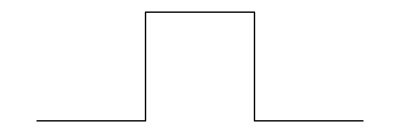

```mathematica
LShow[ "F+F-F-F+F" ]
```

## same as above, plus a list of colors for each segment contained in 'templist' -- unfortunately, 'templist' isn't really 'temp', but stays in memory as a global variable; so sue me

```mathematica
LShowColor[lstring_String, Ldelta_:N[90 Degree]] := (Lpos = {0., 0.}; Ltheta = 0.; templist = Map[ Line, Partition[ Prepend[ DeleteCases[ Map[ Lmove[#, Ldelta]&, Characters[lstring] ], Null], {0,0}], 2,1]]; ncol = N[Length[templist]]; huelist = Table[ Hue[k/ncol], {k, 1., ncol} ]; Show[ Graphics[ N[Flatten[Transpose[{huelist, templist}]]]], AspectRatio -> Automatic]);
```

```mathematica
On[General::spell1];
```

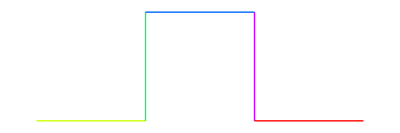

```mathematica
LShowColor[ "F+F-F-F+F" ]
```

```mathematica
LShowColor[ (* Koch curve *)
    LSystem["F", {"F" -> "F+F--F+F"}, 4],
        N[60 Degree]];
```

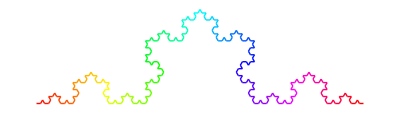

```mathematica
%29
```

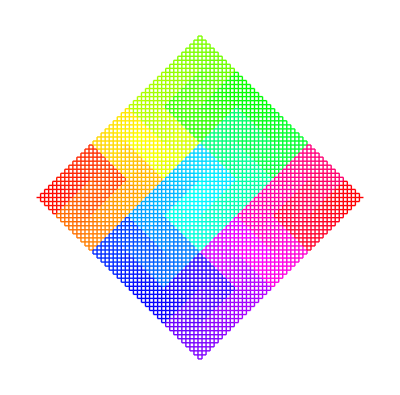

```mathematica
LShowColor[ (* Peano curve *)
    LSystem["F", {"F" -> "F+F-F-F-F+F+F+F-F"}, 4]]
```

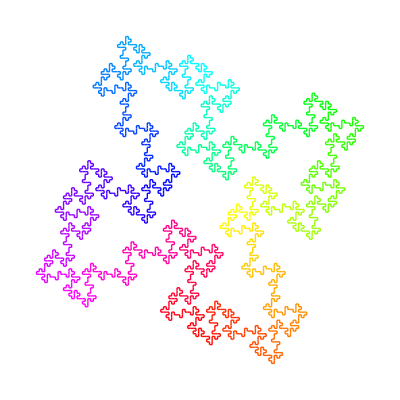

```mathematica
LShowColor[ (* Quadratic Koch island *)
    LSystem["F+F+F+F", {"F" -> "F-F+F+FFF-F-F+F"}, 3]]
```

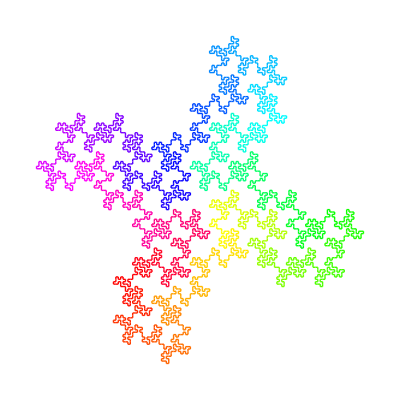

```mathematica
LShowColor[ (* 32-segment curve *)
    LSystem["F+F+F+F",
    {"F" ->
     "-F+F-F-F+F+FF-F+F+FF+F-F-FF+FF-FF+F+F-FF-F-F+FF-F-F+F+F-F+"},
    2]]
```

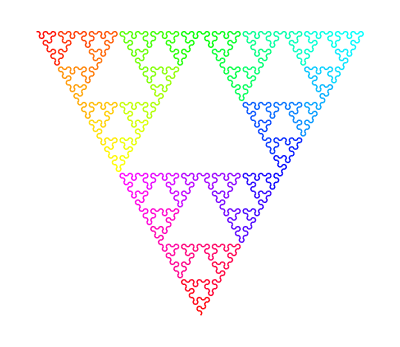

```mathematica
LShowColor[
    LSystem["YF", (* Sierpinski arrowhead *)
     {"X" -> "YF+XF+Y", "Y" -> "XF-YF-X"}, 7],
        N[60 Degree]]
```

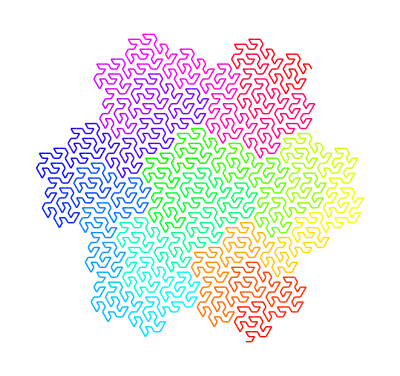

```mathematica
LShowColor[ (* Peano-Gosper curve *)
    LSystem["FX",
      {"X" -> "X+YF++YF-FX--FXFX-YF+",
       "Y" -> "-FX+YFYF++YF+FX--FX-Y"}, 4],
     N[60 Degree]]
```

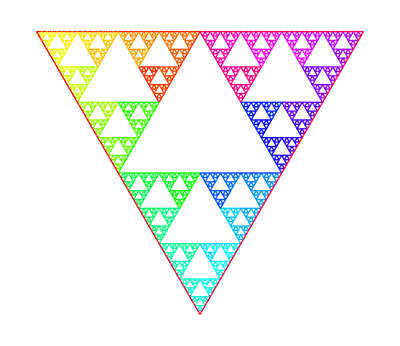

```mathematica
LShowColor[ (* Sierpinski triangle *)
    LSystem["FXF--FF--FF",
    {"F" -> "FF",
     "X"->"--FXF++FXF++FXF--"}, 6], N[60 Degree]]
```

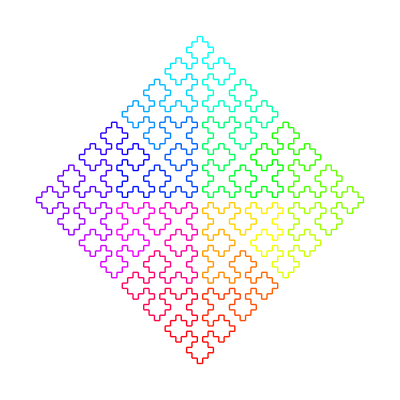

```mathematica
LShowColor@LSystem["F+XF+F+XF", (* Square curve *)
    {"X"->"XF-F+F-XF+F+XF-F+F-X"}, 4]
```

```mathematica
LSystem[ "FX", 
                 {"X"->"X+YF+", "Y"->"-FX-Y"}, 
                 0]
```

FX

```mathematica
LSystem[ "FX", 
                 {"X"->"X+YF+", "Y"->"-FX-Y"}, 
                 1]
```

FX+YF+

```mathematica
LSystem[ "FX", 
                 {"X"->"X+YF+", "Y"->"-FX-Y"}, 
                 2]
```

FX+YF++-FX-YF+

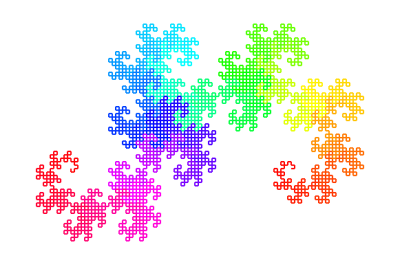

```mathematica
LShowColor[ (* Dragon curve *)
    LSystem["FX", {"X"->"X+YF+", "Y"->"-FX-Y"}, 12]]
```

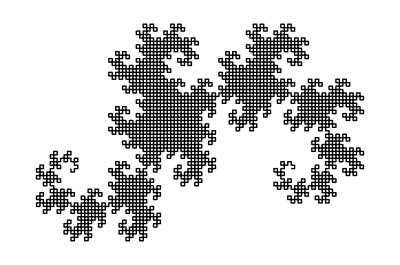

```mathematica
LShow[ (* Dragon curve *)
    LSystem["FX", {"X"->"X+YF+", "Y"->"-FX-Y"}, 12]]
```

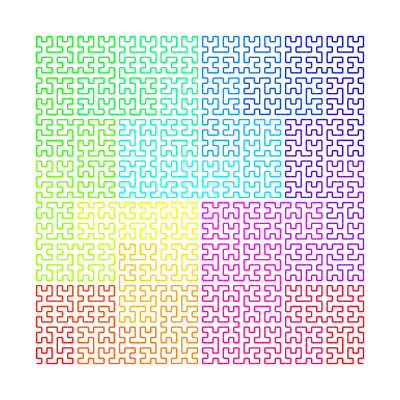

```mathematica
LShowColor@LSystem["L", (* Hilbert curve *)
    {"L" -> "+RF-LFL-FR+", "R" -> "-LF+RFR+FL-"}, 6]
```

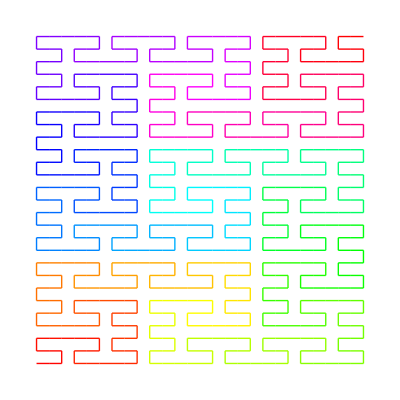

```mathematica
LShowColor@LSystem["X", (* Hilbert curve II *)
    {"X" -> "XFYFX+F+YFXFY-F-XFYFX",
     "Y" -> "YFXFY-F-XFYFX+F+YFXFY"}, 3]
```